```mathematica
ClearAll["Global`*"]
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_,y_]:=Cos[2 π x/L]
Lu[x_,y_]:=-(2 π /L)^2Cos[2 π x/L]
gradu[x_,y_]:={- 2π /L Sin[2 π x/L]}
```

```mathematica
L=1;
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/periodic/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

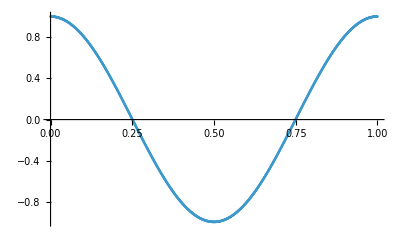

```mathematica
ListPlot[t]
```

```mathematica
δ=Max[Table[Abs[t[[i,3]]-u[t[[i,1]],t[[i,2]]]],{i,1,Length[t]}]]
```

9.65721×10^-7

```mathematica
plotexact=Plot3D[u[x,y],{x,0,L},{y,0,h},PlotRange->Full]
```

-Graphics3D-

```mathematica
plotnum=ListPointPlot3D[t,PlotRange->Full,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
Show[plotexact,plotnum]
```

-Graphics3D-